## Original Jack’s car rental problem

Random variables:
Returns at location A: X_A~PoissonDistribution[3]
Returns at location B: X_B~PoissonDistribution[2]
Rental requests at location A: Y_A~PoissonDistribution[3]
Rental requests at location B: Y_B~PoissonDistribution[4]

End of day n: state is s=(i,j)
Action a is taken: state is (i-a,j+a), where -Min[j,5]≤a≤Min[i,5]
Cars are rented during the day: state is (i-a-Min[i-a,Y_A],j+a-Min[j+a,Y_B])
Cars are returned at the end of the day and excess cars are shipped away: state is (Min[i-a-Min[i-a,Y_A]+X_A,20],Min[j+a-Min[j+a,Y_B]+X_B,20])
End of day n+1: state is s'=(i',j')

### Joint distribution p(s',r|s,a)

This computes the joint distribution numerically.

```mathematica
P=Function[{xa,xb,ya,yb},Exp[-12.] 3.^xa/Gamma[xa+1] 2.^xb/Gamma[xb+1] 3.^ya/Gamma[ya+1] 4.^yb/Gamma[yb+1]];
NextState=Function[{xa,xb,ya,yb,i,j,a},{Min[i-a-Min[i-a,ya]+xa,20],Min[j+a-Min[j+a,yb]+xb,20],Min[i-a,ya,20]+Min[j+a,yb,20]}];
cJoint=Compile[{{i,_Integer},{j,_Integer},{a,_Integer}},
Block[{joint=Table[0.0,{21},{21},{41}],ip,jp,r},
If[a>Min[i,5]∨a<-Min[j,5],Return[joint]];
Do[
{ip,jp,r}=NextState[xa,xb,ya,yb,i,j,a];
joint⟦ip+1,jp+1,r+1⟧+=P[xa,xb,ya,yb]
,{xa,0,20},{xb,0,20},{ya,0,20},{yb,0,20}
];
joint
],CompilationOptions->{"InlineExternalDefinitions"->True},CompilationTarget->"C"
];
```

We precompute the whole distribution. This takes ~1min.

```mathematica
SetSharedFunction[Joint]
LaunchKernels[];
ParallelDo[Do[Joint[i,j,a]=cJoint[i,j,a],{a,-Min[j,5],Min[i,5]}],{i,0,20},{j,0,20},Method->"CoarsestGrained"]//AbsoluteTiming
CloseKernels[];
```

{79.3543,Null}

### Policy evaluation

```mathematica
EvaluatePolicy[V0_,Π_,θ_]:=Block[{V=V0,v,Δ=1.0+θ,γ=0.9,a,p,weight},
While[Δ>θ,
Δ=0.0;
weight=Table[10r+γ V⟦ip+1,jp+1⟧,{ip,0,20},{jp,0,20},{r,0,40}];
Do[
v=V⟦i+1,j+1⟧;
a=Π⟦i+1,j+1⟧;
V⟦i+1,j+1⟧=Total[Joint[i,j,a](weight-2Abs[a]),3];
weight⟦i+1,j+1⟧+=γ(V⟦i+1,j+1⟧-v);
Δ=Max[Δ,Abs[v-V⟦i+1,j+1⟧]]
,{i,0,20},{j,0,20}
]
];
V
]
```

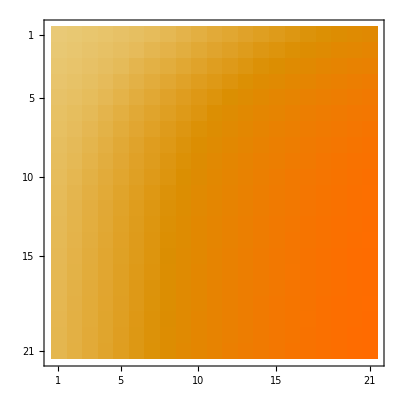
{2.03735,-Graphics-}

```mathematica
EvaluatePolicy[ConstantArray[0.0,{21,21}],ConstantArray[0,{21,21}],0.01]//MatrixPlot//AbsoluteTiming
```

### Policy improvement

```mathematica
ImprovePolicy[V_,Π0_]:=Block[{Π=Π0,γ=0.9,stable,πold,A,joint,weight},
stable=True;
weight=Table[10r+γ V⟦ip+1,jp+1⟧,{ip,0,20},{jp,0,20},{r,0,40}];
Do[
πold=Π⟦i+1,j+1⟧;
A=Table[{a,Total[Joint[i,j,a] (weight-2Abs[a]),3]},{a,-Min[j,5],Min[i,5]}];
Π⟦i+1,j+1⟧=First@First@MaximalBy[Last]@A;
If[Π⟦i+1,j+1⟧≠πold,stable=False];
,{i,0,20},{j,0,20}
];
{stable,Π}
]
```

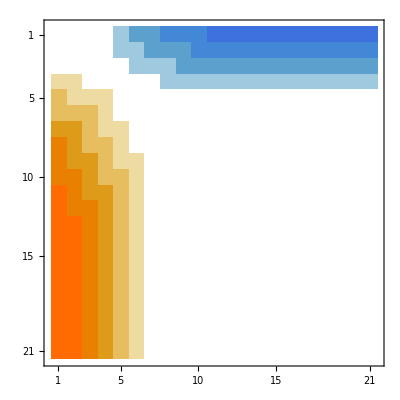
{0.348206,-Graphics-}

```mathematica
ImprovePolicy[ConstantArray[0.0,{21,21}],ConstantArray[0,{21,21}]]//Last//MatrixPlot//AbsoluteTiming
```

### Policy iteration

```mathematica
EstimatePolicy[θ_Real]:=Block[{V,Π,policyStable,Δt,step=1},
V=ConstantArray[500.,{21,21}];
Π=ConstantArray[0,{21,21}];
policyStable=False;
While[¬policyStable,
{Δt,V}=AbsoluteTiming@EvaluatePolicy[V,Π,θ];
Print["Policy evaluation ",step," took ",Δt," sec."];
{Δt,{policyStable,Π}}=AbsoluteTiming@ImprovePolicy[V,Π];
Print["Policy improvement ",step," took ",Δt," sec."];
step+=1;
];
policyPlot=ListContourPlot[Π,Contours->Range[-5,5],ContourLabels->All,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->All,FrameLabel->{"Cars at 2nd location","Cars at 1st location"}];
valuePlot=ListPlot3D[V,PlotRange->All,DataRange->{{0,20},{0,20}},AxesLabel->{"Cars at 1st location","Cars at 2nd location"}];
{V,Π}
]
```

```mathematica
{V,Π}=EstimatePolicy[0.001];
GraphicsRow[{policyPlot,valuePlot}]
```

Policy evaluation 1 took 1.59009 sec.

Policy improvement 1 took 0.365234 sec.

Policy evaluation 2 took 2.36908 sec.

Policy improvement 2 took 0.802488 sec.

Policy evaluation 3 took 2.00369 sec.

Policy improvement 3 took 0.3756 sec.

Policy evaluation 4 took 0.609396 sec.

Policy improvement 4 took 0.362702 sec.

Policy evaluation 5 took 0.226694 sec.

Policy improvement 5 took 0.389463 sec.

-Graphics-

## Modified Jack’s car rental problem

Same problem with the following changes:
One car transfer from A to B is free per night.
Overnight storage of more than 10 cars costs $4.

```mathematica
EvaluatePolicy[V0_,Π_,θ_]:=Block[{V=V0,v,Δ=1.0+θ,γ=0.9,a,weights},
While[Δ>θ,
Δ=0.0;
weights=Table[10r-2Abs[If[a>0,a-1,a]]-If[ip-a>10,4,0]-If[jp+a>10,4,0]+γ V⟦ip+1,jp+1⟧,{a,-5,5},{ip,0,20},{jp,0,20},{r,0,40}];
Do[
v=V⟦i+1,j+1⟧;
a=Π⟦i+1,j+1⟧;
V⟦i+1,j+1⟧=Total[Joint[i,j,a]weights⟦a+6⟧,3];
weights⟦a+6,i+1,j+1⟧+=γ(V⟦i+1,j+1⟧-v);
Δ=Max[Δ,Abs[v-V⟦i+1,j+1⟧]]
,{i,0,20},{j,0,20}
]
];
V
]
```

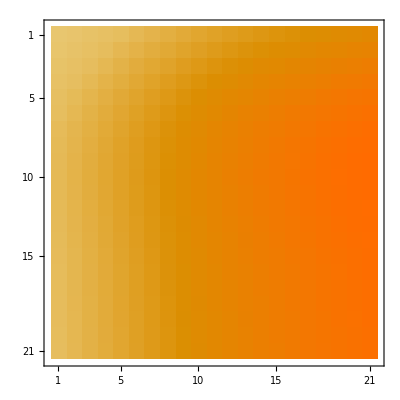
{4.36046,-Graphics-}

```mathematica
EvaluatePolicy[ConstantArray[0.0,{21,21}],ConstantArray[0,{21,21}],0.01]//MatrixPlot//AbsoluteTiming
```

```mathematica
ImprovePolicy[V_,Π0_]:=Block[{Π=Π0,γ=0.9,stable,πold,A,weights},
stable=True;
weights=Table[10r-2Abs[If[a>0,a-1,a]]-If[ip-a>10,4,0]-If[jp+a>10,4,0]+γ V⟦ip+1,jp+1⟧,{a,-5,5},{ip,0,20},{jp,0,20},{r,0,40}];
Do[
πold=Π⟦i+1,j+1⟧;
A=Table[{a,Total[Joint[i,j,a]weights⟦6+a⟧,3]},{a,-Min[j,5],Min[i,5]}];
Π⟦i+1,j+1⟧=First@First@MaximalBy[Last]@A;
If[Π⟦i+1,j+1⟧≠πold,stable=False]
,{i,0,20},{j,0,20}
];
{stable,Π}
]
```

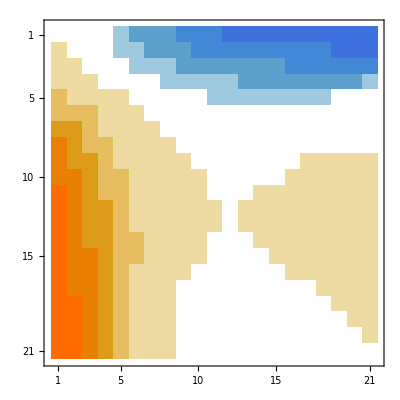
{0.396739,-Graphics-}

```mathematica
ImprovePolicy[ConstantArray[0.0,{21,21}],ConstantArray[0,{21,21}]]//Last//MatrixPlot//AbsoluteTiming
```

```mathematica
{V,Π}=EstimatePolicy[0.001];
GraphicsRow[{policyPlot,valuePlot}]
```

Policy evaluation 1 took 3.77538 sec.

Policy improvement 1 took 0.405469 sec.

Policy evaluation 2 took 5.1698 sec.

Policy improvement 2 took 0.47758 sec.

Policy evaluation 3 took 4.50798 sec.

Policy improvement 3 took 0.490217 sec.

Policy evaluation 4 took 1.87528 sec.

Policy improvement 4 took 0.39718 sec.

Policy evaluation 5 took 0.585091 sec.

Policy improvement 5 took 0.439552 sec.

-Graphics-